## Numerical solution of SRLG+depletion

```mathematica
Nm=13;
μ0=-1.28;
κ=0.01;
```

```mathematica
Clear[μ0]
```

```mathematica
A[ϕ_]:= 2ϕ-1;
B[J_]:= Exp[-J];
```

```mathematica
μ[ϕ_,J_]:=2 Log[A[ϕ] √B[J]+√(1 + A[ϕ]^2(B[J]-1))]-Log[1-A[ϕ]^2]-J;
```

```mathematica
μr[ϕ_,μ0_,nt_]:= μ0 + Log[(nt - Nm ϕ + 1)/nt];
```

### Steady state

```mathematica
sol = ϕ/.NSolve[μ[ϕ,5.00]==μr[ϕ,-4.15,13],ϕ];
sol*Nm
```

{8.19215}

### TDDFT

```mathematica
dΩ[ϕ_,J_,nt_]:= μ[ϕ,J] - μr[ϕ,nt];
```

```mathematica
solRes= NDSolve[{ϕ'[t]==-κ dΩ[ϕ[t],1,10],ϕ[0]==0.01},ϕ,{t,0,200}]
```

{{ϕ→InterpolatingFunction[…]}}

```mathematica
solStall= NDSolve[{ϕ'[t]==-κ dΩ[ϕ[t],1,10],ϕ[0]==0.83},ϕ,{t,0,200}]
```

{{ϕ→InterpolatingFunction[…]}}

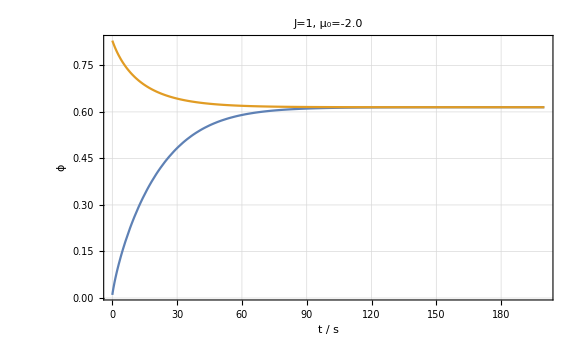

```mathematica
Plot[{Evaluate[ϕ[t]/.solRes],Evaluate[ϕ[t]/.solStall]},{t,0,200},PlotRange-> Full, ImageSize->Large,LabelStyle->{12,GrayLevel[0]}, Frame->True, GridLines->Automatic, FrameLabel->{"t / s","ϕ"}, PlotLabel->"J=1, μ_0=-2.0"]
```